```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
RedC=RGBColor[0.60,0.30,0];
```

## System Hamiltonians

Identity operator

```mathematica
Id[ve_,ho_]:=ve,ho
```

There are two subsystems A and B, each of which are two level systems

```mathematica
HASep[veA_,hoA_,veB_,hoB_]:=({{(ℏ Subscript[ω, 1])/2, 0}, {0, -(ℏ Subscript[ω, 1])/2}})[[veA,hoA]]Id[veB,hoB]
HBSep[veA_,hoA_,veB_,hoB_]:=Id[veA,hoA]({{(ℏ Subscript[ω, 2])/2, 0}, {0, -(ℏ Subscript[ω, 2])/2}})[[veB,hoB]]
```

Eigenstates,
|1>	= |e,e>
|2>	= |e,g>
|3>	= |g,e>
|4>	= |g,g>

Eigenstate mapping function, maps overall state (1 to 4) to subsystem A, B state,

```mathematica
EmapA[i_]:=(i,3+i,4)2+(i,1+i,2)1
EmapB[i_]:=(i,2+i,4)2+(i,1+i,3)1
```

Matrix form of the two Hamiltonians

```mathematica
HA[ve_,ho_]:=HASep[EmapA[ve],EmapA[ho],EmapB[ve],EmapB[ho]]
HB[ve_,ho_]:=HBSep[EmapA[ve],EmapA[ho],EmapB[ve],EmapB[ho]]
```

System Hamiltonians in combined system matrix form

```mathematica
HAMatrix=Table[HA[ve,ho],{ve,1,4},{ho,1,4}];
MatrixForm[HAMatrix]
HBMatrix=Table[HB[ve,ho],{ve,1,4},{ho,1,4}];
MatrixForm[HBMatrix]
```

((ℏ ω_1)/2 | 0 | 0 | 0
0 | (ℏ ω_1)/2 | 0 | 0
0 | 0 | -(ℏ ω_1)/2 | 0
0 | 0 | 0 | -(ℏ ω_1)/2)

((ℏ ω_2)/2 | 0 | 0 | 0
0 | -(ℏ ω_2)/2 | 0 | 0
0 | 0 | (ℏ ω_2)/2 | 0
0 | 0 | 0 | -(ℏ ω_2)/2)

## Interaction Hamiltonian between the two TLSs

Interaction between the two systems are of the form H_int= 1/2 ℏ γ(σ_x^1⊗σ_x^2)

```mathematica
Hint[ve_,ho_]:=(ℏ γ)/2 KroneckerProduct[({{0, 1}, {1, 0}}),({{0, 1}, {1, 0}})][[ve,ho]]
```

```mathematica
HintMatrix:=Table[Hint[ve,ho],{ve,1,4},{ho,1,4}];
MatrixForm[HintMatrix]
```

(0 | 0 | 0 | (γ ℏ)/2
0 | 0 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | 0 | 0
(γ ℏ)/2 | 0 | 0 | 0)

## Combined system Hamiltonian

```mathematica
HtotMatrix=HAMatrix+HBMatrix+HintMatrix;
MatrixForm[HtotMatrix]
```

((ℏ ω_1)/2+(ℏ ω_2)/2 | 0 | 0 | (γ ℏ)/2
0 | (ℏ ω_1)/2-(ℏ ω_2)/2 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | -(ℏ ω_1)/2+(ℏ ω_2)/2 | 0
(γ ℏ)/2 | 0 | 0 | -(ℏ ω_1)/2-(ℏ ω_2)/2)

### Visualize the energy levels of the combined system

```mathematica
unitassum={ℏ->1};
```

#### Bare energy levels without the interaction Hamiltonian

Function for shifting the eigenvalues from Mathematica to our representation

```mathematica
Shift1[i_]:=i,1 4+i,2 2+i,3 3+i,4 1
```

```mathematica
HAHBEVal[i_]:=Eigenvalues[HAMatrix+HBMatrix][[Shift1[i]]]
HAHBEVec[i_]:=Eigenvectors[HAMatrix+HBMatrix][[Shift1[i]]]

Table[{HAHBEVal[i],MatrixForm[HAHBEVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{1/2 ℏ (ω_1-ω_2),(0
1
0
0)},{1/2 ℏ (-ω_1+ω_2),(0
0
1
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

```mathematica
Manipulate[Module[{temp},
temp=Table[HAHBEVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,unitassum}];
Plot[temp,{t,0,2},PlotLegends->{"|1> = |ee>","|2> = |eg>","|3> = |ge>","|4> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic}]
],
Delimiter,Item["Frequencies",Alignment->Center],
{{ω1,1.1},0,3},{{ω2,0.2},0,3}]
```

#### Dressed energy levels with the interaction Hamiltonian

Function for shifting the eigenvalues from Mathematica to our representation

```mathematica
Shift2[i_]:=i,1 4+i,2 2+i,3 1+i,4 3
```

```mathematica
HtotEVal[i_]:=Eigenvalues[HtotMatrix][[Shift2[i]]]
HtotEVec[i_]:=Simplify[Normalize[Eigenvectors[HtotMatrix][[Shift2[i]]]]]

Table[{HtotEVal[i],MatrixForm[HtotEVec[i]]},{i,1,4}]
```

{{1/2 ℏ √(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2),((ω_1+ω_2+√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1+ω_2+√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/γ]^2))
0
0
1/(√(1+Abs[(ω_1+ω_2+√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/γ]^2)))},{1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2),(0
(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
1/(√(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
0)},{-1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2),(0
-(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
1/(√(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
0)},{-1/2 ℏ √(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2),((ω_1+ω_2-√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1+ω_2-√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/γ]^2))
0
0
1/(√(1+Abs[(ω_1+ω_2-√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/γ]^2)))}}

```mathematica
Manipulate[Module[{temp},
temp=Table[HtotEVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}];
{Plot[temp,{t,0,2},PlotLegends->{"|1_DRE> = |ee>","|2_DRE>","|3_DRE>","|4_DRE> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic},ImageSize->Medium]
,Table[MatrixForm[HtotEVec[i]],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}]
}],
Delimiter,Item["Frequencies",Alignment->Center],
{{ω1,1.1},0,3},{{ω2,0.2},0,3},
Delimiter,Item["Interaction strength",Alignment->Center],
{{γs,0.001},0.001,3}]
```

Introducing the interaction Hamiltonian further separates the middle two energy levels.

#### Resonant coupling (i.e. ω_1=ω_2)

```mathematica
Manipulate[Module[{temp},
temp=Table[HtotEVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ωs,Subscript[ω, 2]->ωs,γ->γs,unitassum}];
{Plot[temp,{t,0,2},PlotLegends->{"|1_DRE> = |ee>","|2_DRE>","|3_DRE>","|4_DRE> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic},ImageSize->Medium]
,Table[MatrixForm[HtotEVec[i]],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ωs,Subscript[ω, 2]->ωs,γ->γs,unitassum}]
}],
Delimiter,Item["Frequencies",Alignment->Center],
{{ωs,0.9},0,3},
Delimiter,Item["Interaction strength",Alignment->Center],
{{γs,0.001},0.001,3}]
```

## Representing the system Hamiltonian in new (dressed) |i_DRE>; i=1,2,3,4 basis

Bare eigensystem (without interaction)

```mathematica
Table[{HAHBEVal[i],MatrixForm[HAHBEVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{1/2 ℏ (ω_1-ω_2),(0
1
0
0)},{1/2 ℏ (-ω_1+ω_2),(0
0
1
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

Define 
	Detuning  ΔR= (ω_1-ω_2)
	Sum ΔC= (ω_1+ω_2)
	Rabi frequency ΩR = √(γ^2+ (ω_1-ω_2)^2)	
	Counter rotating frequency ΩC = √(γ^2+ (ω_1+ω_2)^2)

```mathematica
ΔΩassum={ΔR->Subscript[ω, 1]-Subscript[ω, 2],ΩR->√(γ^2+Subscript[ω, 1]^2-2 Subscript[ω, 1] Subscript[ω, 2]+Subscript[ω, 2]^2),ΔC->Subscript[ω, 1]+Subscript[ω, 2],ΩC->√(γ^2+Subscript[ω, 1]^2+2 Subscript[ω, 1] Subscript[ω, 2]+Subscript[ω, 2]^2)};
```

Dressed Eigensystem (with interaction)

```mathematica
Table[{HtotEVal[i],MatrixForm[HtotEVec[i]]},{i,1,4}]//.{√(γ^2+Subscript[ω, 1]^2-2 Subscript[ω, 1] Subscript[ω, 2]+Subscript[ω, 2]^2)->ΩR,√(γ^2+Subscript[ω, 1]^2+2 Subscript[ω, 1] Subscript[ω, 2]+Subscript[ω, 2]^2)->ΩC,-Subscript[ω, 1]+Subscript[ω, 2]->-ΔR,Subscript[ω, 1]-Subscript[ω, 2]->ΔR,-Subscript[ω, 1]-Subscript[ω, 2]->-ΔC,Subscript[ω, 1]+Subscript[ω, 2]->ΔC}
```

{{(ΩC ℏ)/2,((ΔC+ΩC)/(γ √(1+Abs[(ΔC+ΩC)/γ]^2))
0
0
1/(√(1+Abs[(ΔC+ΩC)/γ]^2)))},{(ΩR ℏ)/2,(0
(ΔR+ΩR)/(γ √(1+Abs[(ΔR+ΩR)/γ]^2))
1/(√(1+Abs[(ΔR+ΩR)/γ]^2))
0)},{-(ΩR ℏ)/2,(0
-(-ΔR+ΩR)/(γ √(1+Abs[(-ΔR+ΩR)/γ]^2))
1/(√(1+Abs[(-ΔR+ΩR)/γ]^2))
0)},{-(ΩC ℏ)/2,((ΔC-ΩC)/(γ √(1+Abs[(ΔC-ΩC)/γ]^2))
0
0
1/(√(1+Abs[(ΔC-ΩC)/γ]^2)))}}

Simplifying,

```mathematica
({{(ΔC+ΩC)/(γ √(1+Abs[(ΔC+ΩC)/γ]^2))}, {0}, {0}, {1/(√(1+Abs[(ΔC+ΩC)/γ]^2))}})=({{(ΔC+ΩC)/(√(γ^2+Abs[ΔC+ΩC]^2))}, {0}, {0}, {γ/(√(γ^2+Abs[ΔC+ΩC]^2))}}) = 1/(√(γ^2+Abs[ΔC+ΩC]^2))({{ΔC+ΩC}, {0}, {0}, {γ}})
({{0}, {(ΔR+ΩR)/(γ √(1+Abs[(ΔR+ΩR)/γ]^2))}, {1/(√(1+Abs[(ΔR+ΩR)/γ]^2))}, {0}})=({{0}, {(ΔR+ΩR)/(√(γ^2+Abs[ΔR+ΩR]^2))}, {γ/(√(γ^2+Abs[ΔR+ΩR]^2))}, {0}}) = 1/(√(γ^2+Abs[ΔR+ΩR]^2))({{0}, {ΔR+ΩR}, {γ}, {0}})
({{0}, {-(-ΔR+ΩR)/(γ √(1+Abs[(-ΔR+ΩR)/γ]^2))}, {1/(√(1+Abs[(-ΔR+ΩR)/γ]^2))}, {0}})=({{0}, {-(-ΔR+ΩR)/(√(γ^2+Abs[-ΔR+ΩR]^2))}, {γ/(√(γ^2+Abs[-ΔR+ΩR]^2))}, {0}}) = 1/(√(γ^2+Abs[ΩR-ΔR]^2))({{0}, {ΔR-ΩR}, {γ}, {0}})
({{(ΔC-ΩC)/(γ √(1+Abs[(ΔC-ΩC)/γ]^2))}, {0}, {0}, {1/(√(1+Abs[(ΔC-ΩC)/γ]^2))}})=({{(ΔC-ΩC)/(√(γ^2+Abs[ΔC-ΩC]^2))}, {0}, {0}, {γ/(√(γ^2+Abs[ΔC-ΩC]^2))}}) = 1/(√(γ^2+Abs[ΔC-ΩC]^2))({{ΔC-ΩC}, {0}, {0}, {γ}})
```

```mathematica
HtotEValSimp[i_]:={1/2 ℏ ΩC,1/2 ℏ ΩR,-1/2 ℏ ΩR,-1/2 ℏ ΩC}[[i]]
HtotEVecSimp[i_]:={1/(√(γ^2+Abs[ΔC+ΩC]^2))({{ΔC+ΩC}, {0}, {0}, {γ}}), 1/(√(γ^2+Abs[ΔR+ΩR]^2))({{0}, {ΔR+ΩR}, {γ}, {0}}),1/(√(γ^2+Abs[ΩR-ΔR]^2))({{0}, {ΔR-ΩR}, {γ}, {0}}),1/(√(γ^2+Abs[ΔC-ΩC]^2))({{ΔC-ΩC}, {0}, {0}, {γ}})}[[i]]
```

### Diagonalizing the system Hamiltonian

```mathematica
HtotEVecMatrix=Table[HtotEVec[i],{i,1,4}];
```

```mathematica
HtotMatrix//MatrixForm
Simplify[(Inverse[HtotEVecMatrix].DiagonalMatrix[Table[HtotEVal[i],{i,1,4}]].HtotEVecMatrix)]//MatrixForm
```

((ℏ ω_1)/2+(ℏ ω_2)/2 | 0 | 0 | (γ ℏ)/2
0 | (ℏ ω_1)/2-(ℏ ω_2)/2 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | -(ℏ ω_1)/2+(ℏ ω_2)/2 | 0
(γ ℏ)/2 | 0 | 0 | -(ℏ ω_1)/2-(ℏ ω_2)/2)

(1/2 ℏ (ω_1+ω_2) | 0 | 0 | (γ ℏ)/2
0 | 1/2 ℏ (ω_1-ω_2) | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | -1/2 ℏ (ω_1-ω_2) | 0
(γ ℏ)/2 | 0 | 0 | -1/2 ℏ (ω_1+ω_2))

The diagonalization is through a unitary transformation with U being the eigenvector matrix.

Inverting the diagonalization gives the Hamiltonian in the |1_DRE>, |2_DRE>, |3_DRE> and |4_DRE> basis,

```mathematica
HtotDREMatrix=Simplify[HtotEVecMatrix.HtotMatrix.Inverse[HtotEVecMatrix]];
MatrixForm[HtotDREMatrix]
```

(1/2 ℏ √(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2) | 0 | 0 | 0
0 | 1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2) | 0 | 0
0 | 0 | -1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2) | 0
0 | 0 | 0 | -1/2 ℏ √(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))

We will work in this basis from now on.

```mathematica
HtotDRESimpMatrix=({{1/2 ℏ ΩC, 0, 0, 0}, {0, 1/2 ℏ ΩR, 0, 0}, {0, 0, -1/2 ℏ ΩR, 0}, {0, 0, 0, -1/2 ℏ ΩC}});
```

```mathematica
HtotEVecSimpMatrix=Table[HtotEVecSimp[i],{i,1,4}];
```

Verify both eigenvector matrices are physically the same thing

```mathematica
HtotEVecMatrix//MatrixForm
HtotEVecSimpMatrix//MatrixForm
```

((ω_1+ω_2+√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1+ω_2+√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/γ]^2)) | 0 | 0 | 1/(√(1+Abs[(ω_1+ω_2+√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/γ]^2))
0 | (ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 1/(√(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 0
0 | -(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 1/(√(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 0
(ω_1+ω_2-√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1+ω_2-√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/γ]^2)) | 0 | 0 | 1/(√(1+Abs[(ω_1+ω_2-√(γ^2+ω_1^2+2 ω_1 ω_2+ω_2^2))/γ]^2)))

((ΔC+ΩC)/(√(γ^2+Abs[ΔC+ΩC]^2)) | 0 | 0 | γ/(√(γ^2+Abs[ΔC+ΩC]^2))
0 | (ΔR+ΩR)/(√(γ^2+Abs[ΔR+ΩR]^2)) | γ/(√(γ^2+Abs[ΔR+ΩR]^2)) | 0
0 | (ΔR-ΩR)/(√(γ^2+Abs[-ΔR+ΩR]^2)) | γ/(√(γ^2+Abs[-ΔR+ΩR]^2)) | 0
(ΔC-ΩC)/(√(γ^2+Abs[ΔC-ΩC]^2)) | 0 | 0 | γ/(√(γ^2+Abs[ΔC-ΩC]^2)))

We will work in this basis from now on,
	with the Hamiltonian

```mathematica
HtotDRESimpMatrix//MatrixForm
```

((ΩC ℏ)/2 | 0 | 0 | 0
0 | (ΩR ℏ)/2 | 0 | 0
0 | 0 | -(ΩR ℏ)/2 | 0
0 | 0 | 0 | -(ΩC ℏ)/2)

and eigensystem

```mathematica
Shift3[i_]:=i,1 2+i,2 4+i,3 3+i,4 1
```

```mathematica
HtotDRESSimpEVal[i_]:=Eigenvalues[HtotDRESimpMatrix][[Shift3[i]]]
HtotDRESSimpEVec[i_]:=Simplify[Normalize[Eigenvectors[HtotDRESimpMatrix][[Shift3[i]]]]]

Table[{HtotDRESSimpEVal[i],MatrixForm[HtotDRESSimpEVec[i]]},{i,1,4}]
```

{{(ΩC ℏ)/2,(1
0
0
0)},{(ΩR ℏ)/2,(0
1
0
0)},{-(ΩR ℏ)/2,(0
0
1
0)},{-(ΩC ℏ)/2,(0
0
0
1)}}

## Density Matrix

```mathematica
ρDREMatrix[t_]:=Table[Subscript[ρ, ve,ho][t],{ve,1,4},{ho,1,4}]
```

```mathematica
MatrixForm[ρDREMatrix[t]]
```

(ρ_(1,1)[t] | ρ_(1,2)[t] | ρ_(1,3)[t] | ρ_(1,4)[t]
ρ_(2,1)[t] | ρ_(2,2)[t] | ρ_(2,3)[t] | ρ_(2,4)[t]
ρ_(3,1)[t] | ρ_(3,2)[t] | ρ_(3,3)[t] | ρ_(3,4)[t]
ρ_(4,1)[t] | ρ_(4,2)[t] | ρ_(4,3)[t] | ρ_(4,4)[t])

## Pauli matrices

### In z-base representation

|+z>=(1,0)
|-z>=(0,1)

```mathematica
Subscript[σ, axis_][ve_,ho_]:=axis,1({{0, 1}, {1, 0}})[[ve,ho]]+axis,2({{0, -ⅈ}, {ⅈ, 0}})[[ve,ho]]+axis,3({{1, 0}, {0, -1}})[[ve,ho]];
Id[ve_,ho_]:=ve,ho
```

```mathematica
{Table[Subscript[σ, 1][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 2][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 3][ve,ho],{ve,1,2},{ho,1,2}]};
Map[MatrixForm,%,1]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

### In compound system representation

```mathematica
Subscript[σ, P_,axis_][ve_,ho_]:=
P,1(Subscript[σ, axis][EmapA[ve],EmapA[ho]]Id[EmapB[ve],EmapB[ho]])+
P,2(Id[EmapA[ve],EmapA[ho]]Subscript[σ, axis][EmapB[ve],EmapB[ho]])

Subscript[σMatrix, P_,axis_]:=Table[Subscript[σ, P,axis][ve,ho],{ve,1,4},{ho,1,4}]
Subscript[σPMatrix, P_]:=1/2(Subscript[σMatrix, P,1]+ⅈ Subscript[σMatrix, P,2])
Subscript[σMMatrix, P_]:=1/2(Subscript[σMatrix, P,1]-ⅈ Subscript[σMatrix, P,2])
```

```mathematica
{MatrixForm[Subscript[σMatrix, 1,1]],MatrixForm[Subscript[σMatrix, 2,1]]}
```

{(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

### In new |i_DRE> dressed system basis

We put the Pauli matrices through the same unitary transformation we used above to convert HtotMatrix to HtotDREMatrix

```mathematica
Subscript[σDREMatrix, P_,axis_]:=HtotEVecSimpMatrix.Subscript[σMatrix, P,axis].Inverse[HtotEVecSimpMatrix]
Subscript[σPDREMatrix, P_]:=HtotEVecSimpMatrix.Subscript[σPMatrix, P].Inverse[HtotEVecSimpMatrix]
Subscript[σMDREMatrix, P_]:=HtotEVecSimpMatrix.Subscript[σMMatrix, P].Inverse[HtotEVecSimpMatrix]
```

```mathematica
Simplify[{MatrixForm[Subscript[σDREMatrix, 1,1]],MatrixForm[Subscript[σDREMatrix, 2,1]]}]
```

{(0 | ((γ^2-(ΔC+ΩC) (ΔR-ΩR)) √(γ^2+Abs[ΔR+ΩR]^2))/(2 γ ΩR √(γ^2+Abs[ΔC+ΩC]^2)) | ((-γ^2+(ΔC+ΩC) (ΔR+ΩR)) √(γ^2+Abs[ΔR-ΩR]^2))/(2 γ ΩR √(γ^2+Abs[ΔC+ΩC]^2)) | 0
((γ^2-(ΔC-ΩC) (ΔR+ΩR)) √(γ^2+Abs[ΔC+ΩC]^2))/(2 γ ΩC √(γ^2+Abs[ΔR+ΩR]^2)) | 0 | 0 | ((-γ^2+(ΔC+ΩC) (ΔR+ΩR)) √(γ^2+Abs[ΔC-ΩC]^2))/(2 γ ΩC √(γ^2+Abs[ΔR+ΩR]^2))
((γ^2-(ΔC-ΩC) (ΔR-ΩR)) √(γ^2+Abs[ΔC+ΩC]^2))/(2 γ ΩC √(γ^2+Abs[ΔR-ΩR]^2)) | 0 | 0 | ((-γ^2+(ΔC+ΩC) (ΔR-ΩR)) √(γ^2+Abs[ΔC-ΩC]^2))/(2 γ ΩC √(γ^2+Abs[ΔR-ΩR]^2))
0 | ((γ^2-(ΔC-ΩC) (ΔR-ΩR)) √(γ^2+Abs[ΔR+ΩR]^2))/(2 γ ΩR √(γ^2+Abs[ΔC-ΩC]^2)) | ((-γ^2+(ΔC-ΩC) (ΔR+ΩR)) √(γ^2+Abs[ΔR-ΩR]^2))/(2 γ ΩR √(γ^2+Abs[ΔC-ΩC]^2)) | 0),(0 | ((ΔC-ΔR+ΩC+ΩR) √(γ^2+Abs[ΔR+ΩR]^2))/(2 ΩR √(γ^2+Abs[ΔC+ΩC]^2)) | ((-ΔC+ΔR-ΩC+ΩR) √(γ^2+Abs[ΔR-ΩR]^2))/(2 ΩR √(γ^2+Abs[ΔC+ΩC]^2)) | 0
((-ΔC+ΔR+ΩC+ΩR) √(γ^2+Abs[ΔC+ΩC]^2))/(2 ΩC √(γ^2+Abs[ΔR+ΩR]^2)) | 0 | 0 | ((ΔC-ΔR+ΩC-ΩR) √(γ^2+Abs[ΔC-ΩC]^2))/(2 ΩC √(γ^2+Abs[ΔR+ΩR]^2))
((-ΔC+ΔR+ΩC-ΩR) √(γ^2+Abs[ΔC+ΩC]^2))/(2 ΩC √(γ^2+Abs[ΔR-ΩR]^2)) | 0 | 0 | ((ΔC-ΔR+ΩC+ΩR) √(γ^2+Abs[ΔC-ΩC]^2))/(2 ΩC √(γ^2+Abs[ΔR-ΩR]^2))
0 | ((ΔC-ΔR-ΩC+ΩR) √(γ^2+Abs[ΔR+ΩR]^2))/(2 ΩR √(γ^2+Abs[ΔC-ΩC]^2)) | ((-ΔC+ΔR+ΩC+ΩR) √(γ^2+Abs[ΔR-ΩR]^2))/(2 ΩR √(γ^2+Abs[ΔC-ΩC]^2)) | 0)}

## Calculating positive transition frequencies

Assumptions on energy levels

```mathematica
ωassum={ΩC->2,ΩR->0.1};
```

Transition frequencies,

```mathematica
ω[m_,n_]:=Simplify[(HtotEValSimp[m]-HtotEValSimp[n])/ℏ]
```

Unique and positive transition frequencies,

```mathematica
ω[i_]:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp1 temp3,0][[i]]
]
ωsize:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
Dimensions[DeleteCases[temp1 temp3,0]][[1]]
]
ωplus[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[HtotEValSimp[m],{m,1,4},{n,m+1,4}]];
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
ωminus[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[HtotEValSimp[m],{m,1,4},{n,m+1,4}]];
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
```

```mathematica
Table[ω[i],{i,1,ωsize}]
ωsize
```

{(ΩC-ΩR)/2,(ΩC+ΩR)/2,ΩC,ΩR}

4

## Thermal interactions with the environment

Each of the two TLSs interact thermally with respective thermal baths B_A and B_B with temperatures T_A and T_B.

Interaction Hamiltonian between the thermal bath L or R with the two TLSs is modelled after the Spin-Boson model in the x-component

```mathematica
Subscript[H, TLS-bath]^P=ℏ Subscript[σ, X]^P∑_k Subscript[g, k](Subscript[a, k]^P+Subscript[a, k]^P†)
```

To get the Lindbladian operators, we use equation (15) of Optically Controlled Quantum Thermal Gate paper.

### Get projection matrices Π(ϵ)

```mathematica
πMatrix[i_]:={({{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}})}[[i]]
```

### Get Lindblad operators A^P(ω)

```mathematica
Subscript[AMatrix, P_][ωs_]:=Simplify[∑_(i=1)^4 ∑_(j=1)^4 ωs,ω[i,j](πMatrix[j].Subscript[σDREMatrix, P,1].πMatrix[i]),Assumptions->{ΩR>0,ΩC>0,ΩC>3ΩR}]
```

Lindbladian terms involve a summation of A^P(ω) terms for positive omega.

```mathematica
Table[MatrixForm[Subscript[AMatrix, 1][ω[i]]],{i,1,ωsize}]
Table[MatrixForm[Subscript[AMatrix, 2][ω[i]]],{i,1,ωsize}]
```

{(0 | 0 | 0 | 0
((γ^2-(ΔC-ΩC) (ΔR+ΩR)) √(γ^2+Abs[ΔC+ΩC]^2))/(2 γ ΩC √(γ^2+Abs[ΔR+ΩR]^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | ((-γ^2+(ΔC-ΩC) (ΔR+ΩR)) √(γ^2+Abs[ΔR-ΩR]^2))/(2 γ ΩR √(γ^2+Abs[ΔC-ΩC]^2)) | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
((γ^2-(ΔC-ΩC) (ΔR-ΩR)) √(γ^2+Abs[ΔC+ΩC]^2))/(2 γ ΩC √(γ^2+Abs[ΔR-ΩR]^2)) | 0 | 0 | 0
0 | ((γ^2-(ΔC-ΩC) (ΔR-ΩR)) √(γ^2+Abs[ΔR+ΩR]^2))/(2 γ ΩR √(γ^2+Abs[ΔC-ΩC]^2)) | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

{(0 | 0 | 0 | 0
((-ΔC+ΔR+ΩC+ΩR) √(γ^2+Abs[ΔC+ΩC]^2))/(2 ΩC √(γ^2+Abs[ΔR+ΩR]^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | ((-ΔC+ΔR+ΩC+ΩR) √(γ^2+Abs[ΔR-ΩR]^2))/(2 ΩR √(γ^2+Abs[ΔC-ΩC]^2)) | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
((-ΔC+ΔR+ΩC-ΩR) √(γ^2+Abs[ΔC+ΩC]^2))/(2 ΩC √(γ^2+Abs[ΔR-ΩR]^2)) | 0 | 0 | 0
0 | ((ΔC-ΔR-ΩC+ΩR) √(γ^2+Abs[ΔR+ΩR]^2))/(2 ΩR √(γ^2+Abs[ΔC-ΩC]^2)) | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

Define new values η1, η2, η3 and η4

```mathematica
η1 == ((γ^2-(ΔC-ΩC) (ΔR+ΩR)) √(γ^2+Abs[ΔC+ΩC]^2))/(2 γ ΩC √(γ^2+Abs[ΔR+ΩR]^2)) = - ((-γ^2+(ΔC-ΩC) (ΔR+ΩR)) √(γ^2+Abs[ΔR-ΩR]^2))/(2 γ ΩR √(γ^2+Abs[ΔC-ΩC]^2))
η2 == ((γ^2-(ΔC-ΩC) (ΔR-ΩR)) √(γ^2+Abs[ΔC+ΩC]^2))/(2 γ ΩC √(γ^2+Abs[ΔR-ΩR]^2)) = ((γ^2-(ΔC-ΩC) (ΔR-ΩR)) √(γ^2+Abs[ΔR+ΩR]^2))/(2 γ ΩR √(γ^2+Abs[ΔC-ΩC]^2))
η3 == ((-ΔC+ΔR+ΩC+ΩR) √(γ^2+Abs[ΔC+ΩC]^2))/(2 ΩC √(γ^2+Abs[ΔR+ΩR]^2)) = ((-ΔC+ΔR+ΩC+ΩR) √(γ^2+Abs[ΔR-ΩR]^2))/(2 ΩR √(γ^2+Abs[ΔC-ΩC]^2))
η4 == ((ΔC-ΔR-ΩC+ΩR) √(γ^2+Abs[ΔR+ΩR]^2))/(2 ΩR √(γ^2+Abs[ΔC-ΩC]^2)) = -((-ΔC+ΔR+ΩC-ΩR) √(γ^2+Abs[ΔC+ΩC]^2))/(2 ΩC √(γ^2+Abs[ΔR-ΩR]^2))
```

```mathematica
ηassum={η1->((γ^2-(ΔC-ΩC) (ΔR+ΩR)) √(γ^2+Abs[ΔC+ΩC]^2))/(2 γ ΩC √(γ^2+Abs[ΔR+ΩR]^2)),η2->((γ^2-(ΔC-ΩC) (ΔR-ΩR)) √(γ^2+Abs[ΔC+ΩC]^2))/(2 γ ΩC √(γ^2+Abs[ΔR-ΩR]^2)),η3->((-ΔC+ΔR+ΩC+ΩR) √(γ^2+Abs[ΔC+ΩC]^2))/(2 ΩC √(γ^2+Abs[ΔR+ΩR]^2)),η4->((ΔC-ΔR-ΩC+ΩR) √(γ^2+Abs[ΔR+ΩR]^2))/(2 ΩR √(γ^2+Abs[ΔC-ΩC]^2))};
```

```mathematica
Manipulate[Module[{temp},{
temp=Table[MatrixForm[Subscript[AMatrix, 1][ω[i]]],{i,1,ωsize}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,ΔR->ω1-ω2,ΩR->√(γs^2+(ω1-ω2)^2),ΔC->ω1+ω2,ΩC->√(γs^2+(ω1+ω2)^2),unitassum}],
temp=Table[MatrixForm[Subscript[AMatrix, 2][ω[i]]],{i,1,ωsize}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,ΔR->ω1-ω2,ΩR->√(γs^2+(ω1-ω2)^2),ΔC->ω1+ω2,ΩC->√(γs^2+(ω1+ω2)^2),unitassum}],
{η1,η2,η3,η4}//.Flatten[{ηassum,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,ΔR->ω1-ω2,ΩR->√(γs^2+(ω1-ω2)^2),ΔC->ω1+ω2,ΩC->√(γs^2+(ω1+ω2)^2),unitassum}]
}],
Delimiter,Item["Frequencies",Alignment->Center],
{{ω1,1.1},0,3},
{{ω2,0.2},0,3},
Delimiter,Item["Interaction strength",Alignment->Center],
{{γs,0.001},0.001,3}]
```

```mathematica
Subscript[AMatrixSimp, 1][ω[1]]=({{0, 0, 0, 0}, {η1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, -η1, 0}});Subscript[AMatrixSimp, 1][ω[2]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {η2, 0, 0, 0}, {0, η2, 0, 0}});Subscript[AMatrixSimp, 1][ω[3]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});Subscript[AMatrixSimp, 1][ω[4]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Subscript[AMatrixSimp, 2][ω[1]]=({{0, 0, 0, 0}, {η3, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, η3, 0}});Subscript[AMatrixSimp, 2][ω[2]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {-η4, 0, 0, 0}, {0, η4, 0, 0}});Subscript[AMatrixSimp, 2][ω[3]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});Subscript[AMatrixSimp, 2][ω[4]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

### Calculate Lindbladian terms

Linbladian for the Markovian quantum master equation,

```mathematica
Subscript[LinMatrix, P_][ρ_]:=Simplify[∑_(i=1)^ωsize (Subscript[J, P][ω[i]](1+Subscript[NBE, P][ω[i]])(Subscript[AMatrixSimp, P][ω[i]].ρ.Subscript[AMatrixSimp, P][ω[i]]†-1/2(Subscript[AMatrixSimp, P][ω[i]]†.Subscript[AMatrixSimp, P][ω[i]].ρ+ρ.Subscript[AMatrixSimp, P][ω[i]]†.Subscript[AMatrixSimp, P][ω[i]]))+Subscript[J, P][ω[i]]Subscript[NBE, P][ω[i]](Subscript[AMatrixSimp, P][ω[i]]†.ρ.Subscript[AMatrixSimp, P][ω[i]]-1/2(Subscript[AMatrixSimp, P][ω[i]].Subscript[AMatrixSimp, P][ω[i]]†.ρ+ρ.Subscript[AMatrixSimp, P][ω[i]].Subscript[AMatrixSimp, P][ω[i]]†))),Assumptions->{η1>0,η2>0,η3>0,η4>0}]
```

Net thermal decaying rate Τ_P[i,j] from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_P[i,j] is used due to variable naming issues.

```mathematica
Subscript[Τs, P_][i_,j_]:=Subscript[J, P][ω[i,j]](1+Subscript[NBE, P][ω[i,j]])Subscript[ρ, i,i][t]-Subscript[J, P][ω[i,j]]Subscript[NBE, P][ω[i,j]]Subscript[ρ, j,j][t]
```

Mathematica function for arithmetically proper replacements,

```mathematica
ReplaceArithmetically[expr_,orig_,repl_]:=
Module[{f},
(*Actual replacement function, but it is not Listable*)
f[exprs_,origs_,repls_]:=Module[{q,r},
{q,r}=PolynomialReduce[exprs,origs,{}];
q.repls+r
];
(*Construct for making the function Listable in only the first argument*)
Function[t,f[t,orig,repl],{Listable}][expr]
]
```

```mathematica
ReplaceArithmetically[Subscript[LinMatrix, 1][ρDREMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],{η1^2,η2^2,η3^2,η4^2},Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Table[J[ ω[i]],{i,1,ωsize}]]&]&];
MatrixForm[%]
ReplaceArithmetically[Subscript[LinMatrix, 2][ρDREMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],{η1^2,η2^2,η3^2,η4^2},Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Table[J[ ω[i]],{i,1,ωsize}]]&]&];
MatrixForm[%]
```

(-η1^2 Τ_1[1,2]-η2^2 Τ_1[1,3] | η1^2 (-1/2 J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(1,2)[t]+η2^2 ((-J_1[(ΩC+ΩR)/2]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(1,2)[t]+J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2] ρ_(3,4)[t]) | η2^2 (-1/2 J_1[(ΩC+ΩR)/2]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(1,3)[t]+η1^2 ((-J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(1,3)[t]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2] ρ_(2,4)[t]) | η1^2 (-1/2 J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(1,4)[t]+η2^2 (-1/2 J_1[(ΩC+ΩR)/2]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(1,4)[t]
η1^2 (-1/2 J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(2,1)[t]+η2^2 ((-J_1[(ΩC+ΩR)/2]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(2,1)[t]+J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2] ρ_(4,3)[t]) | η1^2 Τ_1[1,2]-η2^2 Τ_1[2,4] | η1^2 (-1/2 J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(2,3)[t]+η2^2 (-1/2 J_1[(ΩC+ΩR)/2]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(2,3)[t] | η2^2 (-1/2 J_1[(ΩC+ΩR)/2]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(2,4)[t]+η1^2 ((-J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(1,3)[t]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2] ρ_(2,4)[t])
η2^2 (-1/2 J_1[(ΩC+ΩR)/2]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(3,1)[t]+η1^2 ((-J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(3,1)[t]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2] ρ_(4,2)[t]) | η1^2 (-1/2 J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(3,2)[t]+η2^2 (-1/2 J_1[(ΩC+ΩR)/2]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(3,2)[t] | η2^2 Τ_1[1,3]-η1^2 Τ_1[3,4] | η1^2 (-1/2 J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(3,4)[t]+η2^2 ((J_1[(ΩC+ΩR)/2]+J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(1,2)[t]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2] ρ_(3,4)[t])
η1^2 (-1/2 J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(4,1)[t]+η2^2 (-1/2 J_1[(ΩC+ΩR)/2]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(4,1)[t] | η2^2 (-1/2 J_1[(ΩC+ΩR)/2]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(4,2)[t]+η1^2 ((-J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(3,1)[t]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2] ρ_(4,2)[t]) | η1^2 (-1/2 J_1[(ΩC-ΩR)/2]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2]) ρ_(4,3)[t]+η2^2 ((J_1[(ΩC+ΩR)/2]+J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2]) ρ_(2,1)[t]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2] ρ_(4,3)[t]) | η2^2 Τ_1[2,4]+η1^2 Τ_1[3,4])

(-η3^2 Τ_2[1,2]-η4^2 Τ_2[1,3] | η3^2 (-1/2 J_2[(ΩC-ΩR)/2]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(1,2)[t]+η4^2 ((-J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(1,2)[t]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2] ρ_(3,4)[t]) | η4^2 (-1/2 J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(1,3)[t]+η3^2 ((-J_2[(ΩC-ΩR)/2]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(1,3)[t]+J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2] ρ_(2,4)[t]) | η3^2 (-1/2 J_2[(ΩC-ΩR)/2]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(1,4)[t]+η4^2 (-1/2 J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(1,4)[t]
η3^2 (-1/2 J_2[(ΩC-ΩR)/2]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(2,1)[t]+η4^2 ((-J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(2,1)[t]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2] ρ_(4,3)[t]) | η3^2 Τ_2[1,2]-η4^2 Τ_2[2,4] | η3^2 (-1/2 J_2[(ΩC-ΩR)/2]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(2,3)[t]+η4^2 (-1/2 J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(2,3)[t] | η4^2 (-1/2 J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(2,4)[t]+η3^2 ((J_2[(ΩC-ΩR)/2]+J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(1,3)[t]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2] ρ_(2,4)[t])
η4^2 (-1/2 J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(3,1)[t]+η3^2 ((-J_2[(ΩC-ΩR)/2]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(3,1)[t]+J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2] ρ_(4,2)[t]) | η3^2 (-1/2 J_2[(ΩC-ΩR)/2]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(3,2)[t]+η4^2 (-1/2 J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(3,2)[t] | η4^2 Τ_2[1,3]-η3^2 Τ_2[3,4] | η3^2 (-1/2 J_2[(ΩC-ΩR)/2]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(3,4)[t]+η4^2 ((-J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(1,2)[t]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2] ρ_(3,4)[t])
η3^2 (-1/2 J_2[(ΩC-ΩR)/2]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(4,1)[t]+η4^2 (-1/2 J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(4,1)[t] | η4^2 (-1/2 J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(4,2)[t]+η3^2 ((J_2[(ΩC-ΩR)/2]+J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(3,1)[t]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2] ρ_(4,2)[t]) | η3^2 (-1/2 J_2[(ΩC-ΩR)/2]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2]) ρ_(4,3)[t]+η4^2 ((-J_2[(ΩC+ΩR)/2]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2]) ρ_(2,1)[t]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2] ρ_(4,3)[t]) | η4^2 Τ_2[2,4]+η3^2 Τ_2[3,4])

## Quantum Markovian master equation

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, P_][ω_]->Subscript[κ, P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
RHS=Subscript[LinMatrix, 1][ρDREMatrix[t]]+Subscript[LinMatrix, 2][ρDREMatrix[t]];
MatrixForm[%]
```

(-η1^2 J_1[(ΩC-ΩR)/2] ((1+NBE_1[(ΩC-ΩR)/2]) ρ_(1,1)[t]-NBE_1[(ΩC-ΩR)/2] ρ_(2,2)[t])-η3^2 J_2[(ΩC-ΩR)/2] ((1+NBE_2[(ΩC-ΩR)/2]) ρ_(1,1)[t]-NBE_2[(ΩC-ΩR)/2] ρ_(2,2)[t])-η2^2 J_1[(ΩC+ΩR)/2] ((1+NBE_1[(ΩC+ΩR)/2]) ρ_(1,1)[t]-NBE_1[(ΩC+ΩR)/2] ρ_(3,3)[t])-η4^2 J_2[(ΩC+ΩR)/2] ((1+NBE_2[(ΩC+ΩR)/2]) ρ_(1,1)[t]-NBE_2[(ΩC+ΩR)/2] ρ_(3,3)[t]) | -1/2 η1^2 J_1[(ΩC-ΩR)/2] (1+2 NBE_1[(ΩC-ΩR)/2]) ρ_(1,2)[t]-1/2 η3^2 J_2[(ΩC-ΩR)/2] (1+2 NBE_2[(ΩC-ΩR)/2]) ρ_(1,2)[t]-η2^2 J_1[(ΩC+ΩR)/2] ((1+NBE_1[(ΩC+ΩR)/2]) ρ_(1,2)[t]-NBE_1[(ΩC+ΩR)/2] ρ_(3,4)[t])-η4^2 J_2[(ΩC+ΩR)/2] ((1+NBE_2[(ΩC+ΩR)/2]) ρ_(1,2)[t]+NBE_2[(ΩC+ΩR)/2] ρ_(3,4)[t]) | -1/2 η2^2 J_1[(ΩC+ΩR)/2] (1+2 NBE_1[(ΩC+ΩR)/2]) ρ_(1,3)[t]-1/2 η4^2 J_2[(ΩC+ΩR)/2] (1+2 NBE_2[(ΩC+ΩR)/2]) ρ_(1,3)[t]-η1^2 J_1[(ΩC-ΩR)/2] ((1+NBE_1[(ΩC-ΩR)/2]) ρ_(1,3)[t]+NBE_1[(ΩC-ΩR)/2] ρ_(2,4)[t])-η3^2 J_2[(ΩC-ΩR)/2] ((1+NBE_2[(ΩC-ΩR)/2]) ρ_(1,3)[t]-NBE_2[(ΩC-ΩR)/2] ρ_(2,4)[t]) | -1/2 (η1^2 J_1[(ΩC-ΩR)/2] (1+2 NBE_1[(ΩC-ΩR)/2])+η2^2 J_1[(ΩC+ΩR)/2] (1+2 NBE_1[(ΩC+ΩR)/2])) ρ_(1,4)[t]-1/2 (η3^2 J_2[(ΩC-ΩR)/2] (1+2 NBE_2[(ΩC-ΩR)/2])+η4^2 J_2[(ΩC+ΩR)/2] (1+2 NBE_2[(ΩC+ΩR)/2])) ρ_(1,4)[t]
-1/2 η1^2 J_1[(ΩC-ΩR)/2] (1+2 NBE_1[(ΩC-ΩR)/2]) ρ_(2,1)[t]-1/2 η3^2 J_2[(ΩC-ΩR)/2] (1+2 NBE_2[(ΩC-ΩR)/2]) ρ_(2,1)[t]-η2^2 J_1[(ΩC+ΩR)/2] ((1+NBE_1[(ΩC+ΩR)/2]) ρ_(2,1)[t]-NBE_1[(ΩC+ΩR)/2] ρ_(4,3)[t])-η4^2 J_2[(ΩC+ΩR)/2] ((1+NBE_2[(ΩC+ΩR)/2]) ρ_(2,1)[t]+NBE_2[(ΩC+ΩR)/2] ρ_(4,3)[t]) | η1^2 J_1[(ΩC-ΩR)/2] ((1+NBE_1[(ΩC-ΩR)/2]) ρ_(1,1)[t]-NBE_1[(ΩC-ΩR)/2] ρ_(2,2)[t])+η3^2 J_2[(ΩC-ΩR)/2] ((1+NBE_2[(ΩC-ΩR)/2]) ρ_(1,1)[t]-NBE_2[(ΩC-ΩR)/2] ρ_(2,2)[t])-η2^2 J_1[(ΩC+ΩR)/2] ((1+NBE_1[(ΩC+ΩR)/2]) ρ_(2,2)[t]-NBE_1[(ΩC+ΩR)/2] ρ_(4,4)[t])-η4^2 J_2[(ΩC+ΩR)/2] ((1+NBE_2[(ΩC+ΩR)/2]) ρ_(2,2)[t]-NBE_2[(ΩC+ΩR)/2] ρ_(4,4)[t]) | -1/2 (η1^2 J_1[(ΩC-ΩR)/2] (1+2 NBE_1[(ΩC-ΩR)/2])+η2^2 J_1[(ΩC+ΩR)/2] (1+2 NBE_1[(ΩC+ΩR)/2])) ρ_(2,3)[t]-1/2 (η3^2 J_2[(ΩC-ΩR)/2] (1+2 NBE_2[(ΩC-ΩR)/2])+η4^2 J_2[(ΩC+ΩR)/2] (1+2 NBE_2[(ΩC+ΩR)/2])) ρ_(2,3)[t] | -1/2 η2^2 J_1[(ΩC+ΩR)/2] (1+2 NBE_1[(ΩC+ΩR)/2]) ρ_(2,4)[t]-1/2 η4^2 J_2[(ΩC+ΩR)/2] (1+2 NBE_2[(ΩC+ΩR)/2]) ρ_(2,4)[t]-η1^2 J_1[(ΩC-ΩR)/2] ((1+NBE_1[(ΩC-ΩR)/2]) ρ_(1,3)[t]+NBE_1[(ΩC-ΩR)/2] ρ_(2,4)[t])+η3^2 J_2[(ΩC-ΩR)/2] ((1+NBE_2[(ΩC-ΩR)/2]) ρ_(1,3)[t]-NBE_2[(ΩC-ΩR)/2] ρ_(2,4)[t])
-1/2 η2^2 J_1[(ΩC+ΩR)/2] (1+2 NBE_1[(ΩC+ΩR)/2]) ρ_(3,1)[t]-1/2 η4^2 J_2[(ΩC+ΩR)/2] (1+2 NBE_2[(ΩC+ΩR)/2]) ρ_(3,1)[t]-η1^2 J_1[(ΩC-ΩR)/2] ((1+NBE_1[(ΩC-ΩR)/2]) ρ_(3,1)[t]+NBE_1[(ΩC-ΩR)/2] ρ_(4,2)[t])-η3^2 J_2[(ΩC-ΩR)/2] ((1+NBE_2[(ΩC-ΩR)/2]) ρ_(3,1)[t]-NBE_2[(ΩC-ΩR)/2] ρ_(4,2)[t]) | -1/2 (η1^2 J_1[(ΩC-ΩR)/2] (1+2 NBE_1[(ΩC-ΩR)/2])+η2^2 J_1[(ΩC+ΩR)/2] (1+2 NBE_1[(ΩC+ΩR)/2])) ρ_(3,2)[t]-1/2 (η3^2 J_2[(ΩC-ΩR)/2] (1+2 NBE_2[(ΩC-ΩR)/2])+η4^2 J_2[(ΩC+ΩR)/2] (1+2 NBE_2[(ΩC+ΩR)/2])) ρ_(3,2)[t] | η2^2 J_1[(ΩC+ΩR)/2] ((1+NBE_1[(ΩC+ΩR)/2]) ρ_(1,1)[t]-NBE_1[(ΩC+ΩR)/2] ρ_(3,3)[t])+η4^2 J_2[(ΩC+ΩR)/2] ((1+NBE_2[(ΩC+ΩR)/2]) ρ_(1,1)[t]-NBE_2[(ΩC+ΩR)/2] ρ_(3,3)[t])-η1^2 J_1[(ΩC-ΩR)/2] ((1+NBE_1[(ΩC-ΩR)/2]) ρ_(3,3)[t]-NBE_1[(ΩC-ΩR)/2] ρ_(4,4)[t])-η3^2 J_2[(ΩC-ΩR)/2] ((1+NBE_2[(ΩC-ΩR)/2]) ρ_(3,3)[t]-NBE_2[(ΩC-ΩR)/2] ρ_(4,4)[t]) | -1/2 η1^2 J_1[(ΩC-ΩR)/2] (1+2 NBE_1[(ΩC-ΩR)/2]) ρ_(3,4)[t]-1/2 η3^2 J_2[(ΩC-ΩR)/2] (1+2 NBE_2[(ΩC-ΩR)/2]) ρ_(3,4)[t]+η2^2 J_1[(ΩC+ΩR)/2] ((1+NBE_1[(ΩC+ΩR)/2]) ρ_(1,2)[t]-NBE_1[(ΩC+ΩR)/2] ρ_(3,4)[t])-η4^2 J_2[(ΩC+ΩR)/2] ((1+NBE_2[(ΩC+ΩR)/2]) ρ_(1,2)[t]+NBE_2[(ΩC+ΩR)/2] ρ_(3,4)[t])
-1/2 (η1^2 J_1[(ΩC-ΩR)/2] (1+2 NBE_1[(ΩC-ΩR)/2])+η2^2 J_1[(ΩC+ΩR)/2] (1+2 NBE_1[(ΩC+ΩR)/2])) ρ_(4,1)[t]-1/2 (η3^2 J_2[(ΩC-ΩR)/2] (1+2 NBE_2[(ΩC-ΩR)/2])+η4^2 J_2[(ΩC+ΩR)/2] (1+2 NBE_2[(ΩC+ΩR)/2])) ρ_(4,1)[t] | -1/2 η2^2 J_1[(ΩC+ΩR)/2] (1+2 NBE_1[(ΩC+ΩR)/2]) ρ_(4,2)[t]-1/2 η4^2 J_2[(ΩC+ΩR)/2] (1+2 NBE_2[(ΩC+ΩR)/2]) ρ_(4,2)[t]-η1^2 J_1[(ΩC-ΩR)/2] ((1+NBE_1[(ΩC-ΩR)/2]) ρ_(3,1)[t]+NBE_1[(ΩC-ΩR)/2] ρ_(4,2)[t])+η3^2 J_2[(ΩC-ΩR)/2] ((1+NBE_2[(ΩC-ΩR)/2]) ρ_(3,1)[t]-NBE_2[(ΩC-ΩR)/2] ρ_(4,2)[t]) | -1/2 η1^2 J_1[(ΩC-ΩR)/2] (1+2 NBE_1[(ΩC-ΩR)/2]) ρ_(4,3)[t]-1/2 η3^2 J_2[(ΩC-ΩR)/2] (1+2 NBE_2[(ΩC-ΩR)/2]) ρ_(4,3)[t]+η2^2 J_1[(ΩC+ΩR)/2] ((1+NBE_1[(ΩC+ΩR)/2]) ρ_(2,1)[t]-NBE_1[(ΩC+ΩR)/2] ρ_(4,3)[t])-η4^2 J_2[(ΩC+ΩR)/2] ((1+NBE_2[(ΩC+ΩR)/2]) ρ_(2,1)[t]+NBE_2[(ΩC+ΩR)/2] ρ_(4,3)[t]) | η1^2 J_1[(ΩC-ΩR)/2] ((1+NBE_1[(ΩC-ΩR)/2]) ρ_(3,3)[t]-NBE_1[(ΩC-ΩR)/2] ρ_(4,4)[t])+η2^2 J_1[(ΩC+ΩR)/2] ((1+NBE_1[(ΩC+ΩR)/2]) ρ_(2,2)[t]-NBE_1[(ΩC+ΩR)/2] ρ_(4,4)[t])+η3^2 J_2[(ΩC-ΩR)/2] ((1+NBE_2[(ΩC-ΩR)/2]) ρ_(3,3)[t]-NBE_2[(ΩC-ΩR)/2] ρ_(4,4)[t])+η4^2 J_2[(ΩC+ΩR)/2] ((1+NBE_2[(ΩC+ΩR)/2]) ρ_(2,2)[t]-NBE_2[(ΩC+ΩR)/2] ρ_(4,4)[t]))

```mathematica
ReplaceArithmetically[RHS,
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],{η1^2,η2^2,η3^2,η4^2},Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,2}]]]&]&];
MatrixForm[%]
```

(-η1^2 Τ_1[1,2]-η2^2 Τ_1[1,3]-η3^2 Τ_2[1,2]-η4^2 Τ_2[1,3] | η1^2 J_1[(ΩC-ΩR)/2] (-1/2-NBE_1[(ΩC-ΩR)/2]) ρ_(1,2)[t]+η3^2 J_2[(ΩC-ΩR)/2] (-1/2-NBE_2[(ΩC-ΩR)/2]) ρ_(1,2)[t]+η2^2 (J_1[(ΩC+ΩR)/2] (-1-NBE_1[(ΩC+ΩR)/2]) ρ_(1,2)[t]+J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2] ρ_(3,4)[t])+η4^2 (J_2[(ΩC+ΩR)/2] (-1-NBE_2[(ΩC+ΩR)/2]) ρ_(1,2)[t]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2] ρ_(3,4)[t]) | η2^2 J_1[(ΩC+ΩR)/2] (-1/2-NBE_1[(ΩC+ΩR)/2]) ρ_(1,3)[t]+η4^2 J_2[(ΩC+ΩR)/2] (-1/2-NBE_2[(ΩC+ΩR)/2]) ρ_(1,3)[t]+η1^2 (J_1[(ΩC-ΩR)/2] (-1-NBE_1[(ΩC-ΩR)/2]) ρ_(1,3)[t]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2] ρ_(2,4)[t])+η3^2 (J_2[(ΩC-ΩR)/2] (-1-NBE_2[(ΩC-ΩR)/2]) ρ_(1,3)[t]+J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2] ρ_(2,4)[t]) | η1^2 J_1[(ΩC-ΩR)/2] (-1/2-NBE_1[(ΩC-ΩR)/2]) ρ_(1,4)[t]+η2^2 J_1[(ΩC+ΩR)/2] (-1/2-NBE_1[(ΩC+ΩR)/2]) ρ_(1,4)[t]+η3^2 J_2[(ΩC-ΩR)/2] (-1/2-NBE_2[(ΩC-ΩR)/2]) ρ_(1,4)[t]+η4^2 J_2[(ΩC+ΩR)/2] (-1/2-NBE_2[(ΩC+ΩR)/2]) ρ_(1,4)[t]
η1^2 J_1[(ΩC-ΩR)/2] (-1/2-NBE_1[(ΩC-ΩR)/2]) ρ_(2,1)[t]+η3^2 J_2[(ΩC-ΩR)/2] (-1/2-NBE_2[(ΩC-ΩR)/2]) ρ_(2,1)[t]+η2^2 (J_1[(ΩC+ΩR)/2] (-1-NBE_1[(ΩC+ΩR)/2]) ρ_(2,1)[t]+J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2] ρ_(4,3)[t])+η4^2 (J_2[(ΩC+ΩR)/2] (-1-NBE_2[(ΩC+ΩR)/2]) ρ_(2,1)[t]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2] ρ_(4,3)[t]) | η1^2 Τ_1[1,2]-η2^2 Τ_1[2,4]+η3^2 Τ_2[1,2]-η4^2 Τ_2[2,4] | η1^2 J_1[(ΩC-ΩR)/2] (-1/2-NBE_1[(ΩC-ΩR)/2]) ρ_(2,3)[t]+η2^2 J_1[(ΩC+ΩR)/2] (-1/2-NBE_1[(ΩC+ΩR)/2]) ρ_(2,3)[t]+η3^2 J_2[(ΩC-ΩR)/2] (-1/2-NBE_2[(ΩC-ΩR)/2]) ρ_(2,3)[t]+η4^2 J_2[(ΩC+ΩR)/2] (-1/2-NBE_2[(ΩC+ΩR)/2]) ρ_(2,3)[t] | η2^2 J_1[(ΩC+ΩR)/2] (-1/2-NBE_1[(ΩC+ΩR)/2]) ρ_(2,4)[t]+η4^2 J_2[(ΩC+ΩR)/2] (-1/2-NBE_2[(ΩC+ΩR)/2]) ρ_(2,4)[t]+η1^2 (J_1[(ΩC-ΩR)/2] (-1-NBE_1[(ΩC-ΩR)/2]) ρ_(1,3)[t]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2] ρ_(2,4)[t])+η3^2 (J_2[(ΩC-ΩR)/2] (1+NBE_2[(ΩC-ΩR)/2]) ρ_(1,3)[t]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2] ρ_(2,4)[t])
η2^2 J_1[(ΩC+ΩR)/2] (-1/2-NBE_1[(ΩC+ΩR)/2]) ρ_(3,1)[t]+η4^2 J_2[(ΩC+ΩR)/2] (-1/2-NBE_2[(ΩC+ΩR)/2]) ρ_(3,1)[t]+η1^2 (J_1[(ΩC-ΩR)/2] (-1-NBE_1[(ΩC-ΩR)/2]) ρ_(3,1)[t]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2] ρ_(4,2)[t])+η3^2 (J_2[(ΩC-ΩR)/2] (-1-NBE_2[(ΩC-ΩR)/2]) ρ_(3,1)[t]+J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2] ρ_(4,2)[t]) | η1^2 J_1[(ΩC-ΩR)/2] (-1/2-NBE_1[(ΩC-ΩR)/2]) ρ_(3,2)[t]+η2^2 J_1[(ΩC+ΩR)/2] (-1/2-NBE_1[(ΩC+ΩR)/2]) ρ_(3,2)[t]+η3^2 J_2[(ΩC-ΩR)/2] (-1/2-NBE_2[(ΩC-ΩR)/2]) ρ_(3,2)[t]+η4^2 J_2[(ΩC+ΩR)/2] (-1/2-NBE_2[(ΩC+ΩR)/2]) ρ_(3,2)[t] | η2^2 Τ_1[1,3]-η1^2 Τ_1[3,4]+η4^2 Τ_2[1,3]-η3^2 Τ_2[3,4] | η1^2 J_1[(ΩC-ΩR)/2] (-1/2-NBE_1[(ΩC-ΩR)/2]) ρ_(3,4)[t]+η3^2 J_2[(ΩC-ΩR)/2] (-1/2-NBE_2[(ΩC-ΩR)/2]) ρ_(3,4)[t]+η2^2 (J_1[(ΩC+ΩR)/2] (1+NBE_1[(ΩC+ΩR)/2]) ρ_(1,2)[t]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2] ρ_(3,4)[t])+η4^2 (J_2[(ΩC+ΩR)/2] (-1-NBE_2[(ΩC+ΩR)/2]) ρ_(1,2)[t]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2] ρ_(3,4)[t])
η1^2 J_1[(ΩC-ΩR)/2] (-1/2-NBE_1[(ΩC-ΩR)/2]) ρ_(4,1)[t]+η2^2 J_1[(ΩC+ΩR)/2] (-1/2-NBE_1[(ΩC+ΩR)/2]) ρ_(4,1)[t]+η3^2 J_2[(ΩC-ΩR)/2] (-1/2-NBE_2[(ΩC-ΩR)/2]) ρ_(4,1)[t]+η4^2 J_2[(ΩC+ΩR)/2] (-1/2-NBE_2[(ΩC+ΩR)/2]) ρ_(4,1)[t] | η2^2 J_1[(ΩC+ΩR)/2] (-1/2-NBE_1[(ΩC+ΩR)/2]) ρ_(4,2)[t]+η4^2 J_2[(ΩC+ΩR)/2] (-1/2-NBE_2[(ΩC+ΩR)/2]) ρ_(4,2)[t]+η1^2 (J_1[(ΩC-ΩR)/2] (-1-NBE_1[(ΩC-ΩR)/2]) ρ_(3,1)[t]-J_1[(ΩC-ΩR)/2] NBE_1[(ΩC-ΩR)/2] ρ_(4,2)[t])+η3^2 (J_2[(ΩC-ΩR)/2] (1+NBE_2[(ΩC-ΩR)/2]) ρ_(3,1)[t]-J_2[(ΩC-ΩR)/2] NBE_2[(ΩC-ΩR)/2] ρ_(4,2)[t]) | η1^2 J_1[(ΩC-ΩR)/2] (-1/2-NBE_1[(ΩC-ΩR)/2]) ρ_(4,3)[t]+η3^2 J_2[(ΩC-ΩR)/2] (-1/2-NBE_2[(ΩC-ΩR)/2]) ρ_(4,3)[t]+η2^2 (J_1[(ΩC+ΩR)/2] (1+NBE_1[(ΩC+ΩR)/2]) ρ_(2,1)[t]-J_1[(ΩC+ΩR)/2] NBE_1[(ΩC+ΩR)/2] ρ_(4,3)[t])+η4^2 (J_2[(ΩC+ΩR)/2] (-1-NBE_2[(ΩC+ΩR)/2]) ρ_(2,1)[t]-J_2[(ΩC+ΩR)/2] NBE_2[(ΩC+ΩR)/2] ρ_(4,3)[t]) | η2^2 Τ_1[2,4]+η1^2 Τ_1[3,4]+η4^2 Τ_2[2,4]+η3^2 Τ_2[3,4])

Left hand side of the Markovian quantum master equation,

```mathematica
LHS=D[ρDREMatrix[t], t];
MatrixForm[%]
```

(ρ_(1,1)'[t] | ρ_(1,2)'[t] | ρ_(1,3)'[t] | ρ_(1,4)'[t]
ρ_(2,1)'[t] | ρ_(2,2)'[t] | ρ_(2,3)'[t] | ρ_(2,4)'[t]
ρ_(3,1)'[t] | ρ_(3,2)'[t] | ρ_(3,3)'[t] | ρ_(3,4)'[t]
ρ_(4,1)'[t] | ρ_(4,2)'[t] | ρ_(4,3)'[t] | ρ_(4,4)'[t])

Markovian quantum master equation for a general density matrix,

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,4},{j,1,4}]]]/.Rule->Equal];
```

```mathematica
Table[J[ ω[i]],{i,1,ωsize}];
Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]];
sol=ApplySides[Collect[Expand[#],{η1^2,η2^2,η3^2,η4^2},Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Table[J[ ω[i]],{i,1,ωsize}]]&]&]&,sol];
```

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;5]];
soloffdiag=Delete[sol,Table[{1+5i},{i,0,3}]];
```

Diagonals of the Markovian quantum master equation simplified to transition rates,

```mathematica
soldiagtran=ApplySides[
ReplaceArithmetically[Simplify[#],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
]&,soldiag]
```

{ρ_(1,1)'[t]==-η1^2 Τ_1[1,2]-η2^2 Τ_1[1,3]-η3^2 Τ_2[1,2]-η4^2 Τ_2[1,3],ρ_(2,2)'[t]==η1^2 Τ_1[1,2]-η2^2 Τ_1[2,4]+η3^2 Τ_2[1,2]-η4^2 Τ_2[2,4],ρ_(3,3)'[t]==η2^2 Τ_1[1,3]-η1^2 Τ_1[3,4]+η4^2 Τ_2[1,3]-η3^2 Τ_2[3,4],ρ_(4,4)'[t]==η2^2 Τ_1[2,4]+η1^2 Τ_1[3,4]+η4^2 Τ_2[2,4]+η3^2 Τ_2[3,4]}

## Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^(ω Subscript[β, P])-1);
```

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 2]->T2}},{ω,0,10 0.2},PlotRange-> {0,2},PlotLegends->{"L","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,0.2},0.01,1},{{T2,0.1},0.01,1}]
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1.38 10^-23,ℏ->1.054 10^-34,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1.38 10^-23,ℏ->1.054 10^-34,Subscript[T, 2]->T2}},{ω,0,10 k/ℏ 300/.{k-> 1.3806 10^-23,ℏ->1.0546 10^-34}},PlotRange-> {0,2},PlotLegends->{"L","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,300},0.01,500},{{T2,150},0.01,500}]
```

Calculate heat current flow,

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Tr[Subscript[LinMatrix, P][ρ].HtotDRESimpMatrix]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowIn, 1][ρDREMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[%,{η1^2,η2^2,η3^2,η4^2},Collect[#,Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]]&]

ReplaceArithmetically[Subscript[EngyFlowIn, 2][ρDREMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[%,{η1^2,η2^2,η3^2,η4^2},Collect[#,Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]]&]
```

η2^2 ((-(ΩC ℏ)/2-(ΩR ℏ)/2) Τ_1[1,3]+(-(ΩC ℏ)/2-(ΩR ℏ)/2) Τ_1[2,4])+η1^2 ((-(ΩC ℏ)/2+(ΩR ℏ)/2) Τ_1[1,2]+(-(ΩC ℏ)/2+(ΩR ℏ)/2) Τ_1[3,4])

η4^2 ((-(ΩC ℏ)/2-(ΩR ℏ)/2) Τ_2[1,3]+(-(ΩC ℏ)/2-(ΩR ℏ)/2) Τ_2[2,4])+η3^2 ((-(ΩC ℏ)/2+(ΩR ℏ)/2) Τ_2[1,2]+(-(ΩC ℏ)/2+(ΩR ℏ)/2) Τ_2[3,4])

## On unit conversions

To resolve the natural units to SI units, we use the relationship,
Energy = ℏ ω = k_B T
In the natural units case, we have chosen Ts to be an order of magnitude lower than the largest ωs.

In SI units, T'_H = 400, in natural units, T_H=0.2.
This gives a ratio of T'_H/T_H=2000.

Temperature conversion, T'=2000 T

Frequency conversion,  ω'=(2000 k_B)/ℏ ω, Ω'=(2000 k_B)/ℏ Ω

Time conversion,  t'=ℏ/(2000 k_B)t

Transition rates conversion, Τ'=(2000 k_B)/ℏ Τ

Energy flows conversion, J'=ℏ(2000 k_B)/ℏ(2000 k_B)/ℏ J=(2000 k_B)^2/ℏ J

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

Unit conversion factors for SI units,

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
```

```mathematica
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations (Removing Quiet functions in code will allow warnings about this issue to be displayed). Hence it is always advisable to confirm simulation results with natural unit simulations.

## Density matrix, transition rate and energy flow evolution with time

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.1 ωconv,Subscript[ω, 2]->0.2 ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

Assumption on the strength of the L-R interaction

```mathematica
γassum={γ->0.001 ωconv};
```

```mathematica
γassum={γ->0.3ωconv};
```

```mathematica
γassum={γ->1ωconv};
```

System energy matrix under above assumptions,

```mathematica
MatrixForm[HtotMatrix//.Flatten[{Tassum,unitassum,γassum}]]
MatrixForm[HtotDREMatrix//.Flatten[{Tassum,unitassum,γassum}]]
```

(0.65 | 0 | 0 | 0.0005
0 | 0.45 | 0.0005 | 0
0 | 0.0005 | -0.45 | 0
0.0005 | 0 | 0 | -0.65)

(0.65 | 0 | 0 | 0
0 | 0.45 | 0 | 0
0 | 0 | -0.45 | 0
0 | 0 | 0 | -0.65)

Numerical solution of the dynamics, with the initial condition that all density matrix elements except the first are zero.

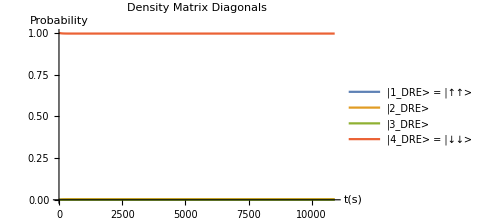

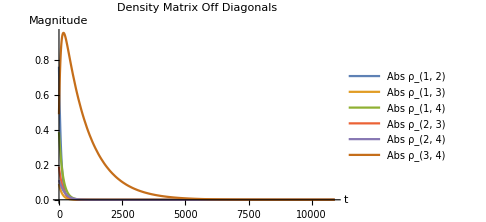
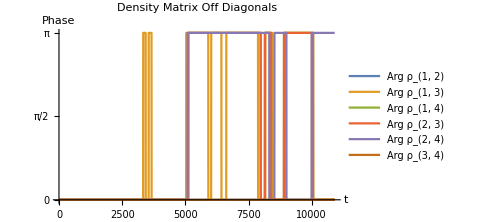

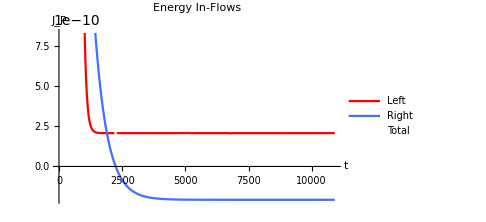

```mathematica
tmax=(120/(Subscript[ω, 1] Subscript[κ, 1]))//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{ΔΩassum,ηassum,γassum,NBEassum,unitassum,Tassum,Jassum}],Table[Subscript[ρ, i,j][0]==i,j i,4 1+∑_(k=2)^4 ∑_(l=1)^(k-1) (i,k j,l RandomReal[]+j,k i,l RandomReal[]),{i,1,4},{j,1,4}]}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,4},{j,1,4}]],{t,0,tmax}
];

Flatten[{Table[Subscript[ρ, i,i][t],{i,1,4}]}/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1_DRE> = |↑↑> "],
		Style["|2_DRE>"],
		Style["|3_DRE>"],
		Style["|4_DRE> = |↓↓> "]}]

plot1=Flatten[{Abs[Subscript[ρ, 1,2][t]],Abs[Subscript[ρ, 1,3][t]],Abs[Subscript[ρ, 1,4][t]],Abs[Subscript[ρ, 2,3][t]],Abs[Subscript[ρ, 2,4][t]],Abs[Subscript[ρ, 3,4][t]]}/.dynamics];
plot2=Flatten[{Arg[Subscript[ρ, 1,2][t]],Arg[Subscript[ρ, 1,3][t]],Arg[Subscript[ρ, 1,4][t]],Arg[Subscript[ρ, 2,3][t]],Arg[Subscript[ρ, 2,4][t]],Arg[Subscript[ρ, 3,4][t]]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange-> Full,
	AxesLabel->{Style["t"],Style["Magnitude"]}, 
	PlotLegends->{
		Style["Abs ρ_(1, 2)"],
		Style["Abs ρ_(1, 3)"],
		Style["Abs ρ_(1, 4)"],
		Style["Abs ρ_(2, 3)"],
		Style["Abs ρ_(2, 4)"],
		Style["Abs ρ_(3, 4)"]}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange->Full,
	AxesLabel->{"t","Phase"}, 
	Ticks->{Automatic,{0,π/2,π}},
	PlotLegends->{
		Style["Arg ρ_(1, 2)"],
		Style["Arg ρ_(1, 3)"],
		Style["Arg ρ_(1, 4)"],
		Style["Arg ρ_(2, 3)"],
		Style["Arg ρ_(2, 4)"],
		Style["Arg ρ_(3, 4)"]}]}

Flatten[{Subscript[EngyFlowIn, 1][ρDREMatrix[t]],Subscript[EngyFlowIn, 2][ρDREMatrix[t]],Subscript[EngyFlowIn, 1][ρDREMatrix[t]]+Subscript[EngyFlowIn, 2][ρDREMatrix[t]]}//.Flatten[{ΔΩassum,ηassum,γassum,NBEassum,unitassum,Tassum,Jassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Energy In-Flows"],
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Right","Total"},
	PlotStyle->{Red,BlueC,{White,Dashed}}]
```

## Density matrix, transition rate and energy flow at equilibrium

Energy flows conversion, J'=ℏ(2000 k_B)/ℏ(2000 k_B)/ℏ J=(2000 k_B)^2/ℏ J

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

Unit conversion factors for SI units,

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
```

```mathematica
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Function for density matrix elements, transition rates and energy flows,

```mathematica
varFunc[T1_,T2_,κ1_,κ2_,ω1_,ω2_,γs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,Jassum,NBEassum,ΔΩassum,ηassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, i_,j_]'[t]->0,Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j]},1==∑_(i=1)^4 Subscript[ρ, i,i]}];
temp3=Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, i,j],{i,1,4},{j,1,4}]]]];
Re[{
Flatten[Table[Subscript[ρ, i,i],{i,1,4}]]/.temp3,
Flatten[{
η1^2 Subscript[Τs, 1][1,2],η2^2 Subscript[Τs, 1][1,3],η2^2 Subscript[Τs, 1][2,4],η1^2 Subscript[Τs, 1][3,4],
η3^2 Subscript[Τs, 2][1,2],η4^2 Subscript[Τs, 2][1,3],η4^2 Subscript[Τs, 2][2,4],η3^2 Subscript[Τs, 2][3,4]
}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3],
Flatten[{
Subscript[EngyFlowIn, 1][ρDREMatrix[t]],Subscript[EngyFlowIn, 2][ρDREMatrix[t]]
}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3],
Table[Subscript[ρ, i,j],{i,1,4},{j,1,4}]//.temp3
}]
]
```

Test function

```mathematica
varFunc[0.2,0.02,1,1,1.1,0.9,0.1,unitassum]
```

{{2.72564×10^-6,0.00364791,0.000743895,0.995605},{-2.32205×10^-6,-1.27959×10^-7,-0.000171256,-0.000633747,2.32205×10^-6,1.27959×10^-7,0.000171256,0.000633747},{0.000756508,-0.000756508},{{2.72564×10^-6,0.,0.,0.},{0.,0.00364791,0.,0.},{0.,0.,0.000743895,0.},{0.,0.,0.,0.995605}}}

Function for drawing a state flow diagram,

```mathematica
DrawFlowGraph[label_,posx_,posy_,nodes_,rates_,ratecolors_,ratesF_,ratecolorsF_,title_,maxrate_]:=Module[{pos,psize},
psize=Dimensions[label][[1]];
pos[i_]:={posx[[i]],posy[[i]]};
Graphics[Flatten[{
{Thickness[0.0001],Arrowheads[0.03],Black,Arrow[{{1.15Min[posx],1.2Min[posy]},{1.15Min[posx],1.1Max[posy]}}]},Black,{Text[Style["Energy",FontSize->13.6,FontFamily->"Times New Roman"],{1.0Min[posx]-0.03,1.15Max[posy]}],Text[Style[title,FontSize->13.6,FontFamily->"Times New Roman"],{0,1.57Min[posy]}]},

Table[{Opacity[1],Thick,RGBColor[0.55,0.55,0.55],Disk[pos[i],0.01+0.22 √nodes[[i]]]},{i,1,psize}],
Table[
	If[rates[[i,j]]≠0 ,
		If[ ratesF[[i,j]]≠0,
			If[Abs[rates[[i,j]]]>Abs[ratesF[[i,j]]],
				{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			,
				{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			]
		,
			{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
			ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		]
	,
		If[ ratesF[[i,j]]≠0,
			{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
			ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		, Nothing]
	]
,{i,1,psize-1},{j,i+1,psize}],
Table[{Opacity[1],Black,Text[Style[label[[i]],FontSize->12],{posx[[i]]+{0,0.04,0,0.06,0.04,0,0.04,0}[[i]],posy[[i]]+{0.045,0.08,-0.05,-0.06,0.06,-0.05,-0.08,0.045}[[i]]}]},{i,1,psize}]

}], ImageSize->Medium]
]

DrawFunc[T1_,T2_,ω1_,ω2_,γs_,title_,maxrate_,var_]:=Module[{label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,temp0},temp0=Flatten[{Jassum,NBEassum,k->1,κ->1,Subscript[T, 1]-> T1,Subscript[T, 2]-> T2,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2}];label={"|1_DRE>=|↑↑>","|2_DRE>","|3_DRE>","|4_DRE>=|↓↓>"};posx={0,-0.4,0.4,0};posy=Diagonal[HtotDREMatrix/(ℏ ωconv)/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}]];nodes=var[[1]];rates=({{0, var[[2]][[1]], var[[2]][[2]], 0}, {0, 0, 0, var[[2]][[3]]}, {0, 0, 0, var[[2]][[4]]}, {0, 0, 0, 0}});
ratesF=({{0, var[[2]][[5]], var[[2]][[6]], 0}, {0, 0, 0, var[[2]][[7]]}, {0, 0, 0, var[[2]][[8]]}, {0, 0, 0, 0}});ratecolors=({{0, Red, RedC, 0}, {0, 0, 0, RedC}, {0, 0, 0, Red}, {0, 0, 0, 0}});
ratecolorsF=({{0, BlueC, Blue, 0}, {0, 0, 0, Blue}, {0, 0, 0, BlueC}, {0, 0, 0, 0}});
DrawFlowGraph[label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,title,maxrate]
]
```

Steady-state energy flows, transition rates, density matrix diagonals and energy eigenvalues, plotted for dynamically changeable bath, and system parameters,

```mathematica
Manipulate[Module[{temp1,temp2,temp3,temp4,ηs,νs,Δs,Ωs},
temp1=varFunc[T1,T2,κ1,κ2,ω1,ω2,γs,unitassum];
temp2=Table[HtotEVal[i],{i,1,4}]/ℏ/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}];
temp3=Inverse[HtotEVecMatrix].temp1[[4]].HtotEVecMatrix/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}];
temp4=temp1[[4]];
Δs=Δ//.Flatten[{ΔΩassum,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
Ωs=Ω//.Flatten[{ΔΩassum,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
ηs=η//.Flatten[{ΔΩassum,ηassum,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
νs=ν//.Flatten[{ΔΩassum,ηassum,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
{
Plot[temp2,{t,0,2},
	ImageSize->Medium,
	PlotLegends->{"|1_DRE> = |↑↑>","|2_DRE>","|3_DRE>","|4_DRE> = |↓↓>"},
	AxesLabel->{None,"Frequency"},
	PlotRange->{-1.5ωconv/.unitassum,1.5 ωconv/.unitassum},
	Ticks->{None,Automatic}],
Table[MatrixForm[HtotEVec[i]],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}],

MatrixForm[({{TextForm["Density Matrix - |↑↑>,|↑↓>,|↓↑>,|↓↓> basis"], TextForm["Density Matrix - |1_DRE>,|2_DRE>,|3_DRE>,|4_DRE> basis"]}, {MatrixForm[temp3], MatrixForm[temp4]}})],

DrawFunc[T1,T2,ω1,ω2,γs,StringForm["ω_1=``, ω_2=``, γ=``,
 Δ=``, Ω=`` 
η=``, ν=``",DecimalForm[ω1,{3,2}],DecimalForm[ω2,{3,2}],DecimalForm[γs,{3,2}],DecimalForm[Δs,{3,2}],DecimalForm[Ωs,{3,2}],DecimalForm[ηs,{3,2}],DecimalForm[νs,{3,2}]],Τmax,temp1],

BarChart[temp1[[3]]
,ChartLabels->{"Left ","Right"},PlotLabel->"Equilibrium energy inflow",AxesLabel->{"","J_P(J)"},ImageSize->Medium,PlotRange->{-Emax,Emax},ChartStyle->{Green,Red}],

BarChart[temp1[[2]]
,ChartLabels->Placed[{"L |1_DRE> to |2_DRE>","L |1_DRE> to |3_DRE>","L |2_DRE> to |4_DRE>","L |3_DRE> to |4_DRE>","R |1_DRE> to |2_DRE>","R |1_DRE> to |3_DRE>","R |2_DRE> to |4_DRE>","R |3_DRE> to |4_DRE>"},Bottom,Rotate[#,π/2]&],PlotLabel->"Equilibrium thermal transition rate",ImageSize->Medium,ChartStyle->{Red,RedC,RedC,Red,BlueC,Blue,Blue,BlueC}],

BarChart[temp1[[1]]
,ChartLabels->{"ρ_{1, 1}","ρ_{2, 2}","ρ_{3, 3}","ρ_{4, 4}"},PlotLabel->"Equilibrium density matrix",ImageSize->Medium,PlotRange->{-0.1,1},ChartStyle->"Pastel"]
}],
Delimiter,Item["Fixed Bath Temperatures",Alignment->Center],
{{T1,0.20 Tconv},0.001 Tconv,1 Tconv},
{{T2,0.02 Tconv},0.001 Tconv,1 Tconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κ1,0.01},0.001,2},
{{κ2,0.01},0.001,2},
Delimiter,Item["System Parameters",Alignment->Center],
{{ω1,1.1ωconv},0ωconv,2ωconv},
{{ω2,0.2ωconv},0ωconv,2ωconv},
{{γs,0.3ωconv},0.001ωconv,2ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax,0.00005Econv},0.00001Econv,0.001Econv},
{{Τmax,0.001Τconv},0.0001Τconv,0.01Τconv},
ContinuousAction->False]
```

## Energy flow characteristics for different system parameters

### Energy flow under different levels of resonance

Energy flows when ω_2 is changed from below ω_1 to above ω_1, keeping γ constant,

```mathematica
PlotEngyFlowsWithω2[T1_,T2_,κ1_,κ2_,ω1s_,ω2min_,ω2max_,γs_,ωres_,legends_]:=Module[{tempx,tempy,temp},
tempx=Table[{ω2,ω2},{ω2,ω2min,ω2max,ωres}];
tempy=10^5 Table[varFunc[T1,T2,κ1,κ2,ω1s,ω2,γs,unitassum],{ω2,ω2min,ω2max,ωres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,3,i]]}],{i,1,2}];
ListPlot[temp,
	PlotRange->{{ω2min,ω2max},Full},
	ImageSize->Medium,
	AxesStyle->Directive[Darker[Gray],13.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["ω2",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->14.5]},
	Joined->True,
	PlotStyle->{{Red},{BlueC}},
	PlotLegends->legends &&{
		Style["J_L",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_R",FontFamily->"Times New Roman",FontSize->14.5]}]
]
```

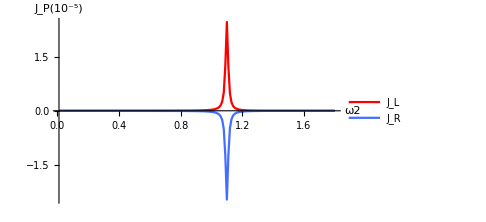
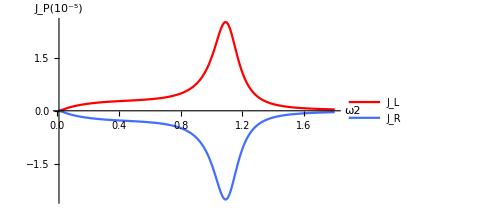
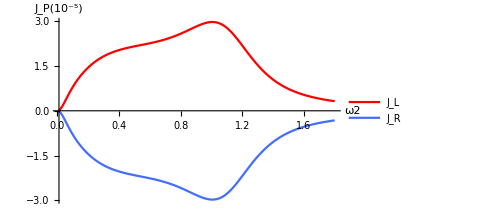

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γs=0.01ωconv;
ω1=1.1ωconv;
ω2min=0.01ωconv;ω2max=1.8ωconv;ωres=0.01ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres,True]
],
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γs=0.1ωconv;
ω1=1.1ωconv;
ω2min=0.01ωconv;ω2max=1.8ωconv;ωres=0.01ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres,True]
],
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γs=0.3ωconv;
ω1=1.1ωconv;
ω2min=0.01ωconv;ω2max=1.8ωconv;ωres=0.01ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres,True]
]
}
```

### Energy flow under different levels of resonance and different coupling strengths

```mathematica
PlotEngyFlowsWithγ[T1_,T2_,κ1_,κ2_,ω1s_,ω2s_,γmin_,γmax_,γres_,legends_]:=Module[{tempx,tempy,temp,p1,p2},
tempx=Table[{γ,γ},{γ,γmin,γmax,γres}];
tempy=10^5 Table[varFunc[T1,T2,κ1,κ2,ω1s,ω2s,γ,unitassum],{γ,γmin,γmax,γres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,3,i]]}],{i,1,2}];
p1=ListPlot[temp,
	PlotRange->{{γmin,γmax},Full},
	ImageSize->Medium,
	AxesStyle->Directive[Darker[Gray],13.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["γ",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->14.5]},
	Joined->True,
	PlotStyle->{{Red},{BlueC}},
	PlotLegends->legends &&{
		Style["J_L with σ_x-σ_x",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_R with σ_x-σ_x",FontFamily->"Times New Roman",FontSize->14.5]}];
p2= Plot[{10^5 0.0000246642,-10^5 0.0000246642},{γ,γmin,γmax},
PlotStyle->{{Red,Dashed},{BlueC,Dashed}},
	PlotLegends->legends &&{
		Style["J_L with B_I",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_R with B_I",FontFamily->"Times New Roman",FontSize->14.5]}];
Show[p1,p2]
]
```

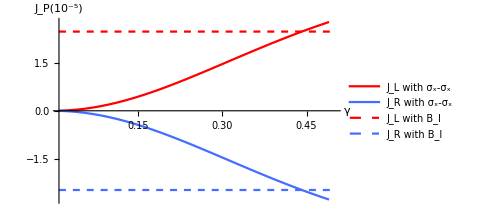

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ω2,γmin,γmax,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.01ωconv;γmax=0.5 ωconv;γres=0.015;
ω1=1.1ωconv;
ω2=0.2ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ω2,γmin,γmax,γres,True]
]
```

```mathematica
PlotEngyFlowsWithω2andγ[T1_,T2_,κ1_,κ2_,ω1s_,ω2min_,ω2max_,γmin_,γmax_,ωres_,γres_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[ω2,{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];
tempy=Table[γ,{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];
tempz=10^5 Table[varFunc[T1,T2,κ1,κ2,ω1s,ω2,γ,unitassum][[3,1]],{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];

temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];

ListPlot3D[temp,
	PlotRange->{{ω2min,ω2max},{γmin,γmax},Full},
	ImageSize->Large,
	AxesStyle->Directive[Black,20.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["ω_2",FontFamily->"Times New Roman",FontSize->20.5],
		Style["γ",FontFamily->"Times New Roman",FontSize->20.5],
		Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->20.5]},
	ColorFunction->"BlueGreenYellow",
Mesh->{Table[ω2,{ω2,ω2min,ω2max,0.1}],Table[γ,{γ,γmin,γmax,0.05}]}]
]
```

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γmin,γmax,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.01ωconv;γmax=0.5 ωconv;γres=0.015;
ω1=1.1ωconv;
ω2min=0.01ωconv;ω2max=1.8ωconv;ωres=0.01ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γmin,γmax,ωres,γres,True]
]
```

-Graphics3D-